# Orthogonality of ''Trigg'' Functions

In the ''Trigg's Equation'' chapter of the guide, the general inner product determining the orthogonality of two functions was introduced in equation (1.16). This equation, restated below:

∫_a^b f[x] g[x] w[x]ⅆx

may initially not feel particularly intuitive. As such, we discussed that orthogonality is similar to the idea of perpendicularity in certain situations. This, however, can be slightly misleading, as some may then expect that two functions are orthogonal if they appear to be perpendicular to one another. Take a simple example of the orthogonality of two sine functions. In the following example, sin(x) will be represented in red, while sin(2x) will be represented in green. We expect that, over the period 2Pi, these functions will be orthogonal, by the orthogonality integral given in equation (1.16). Let's take a look.

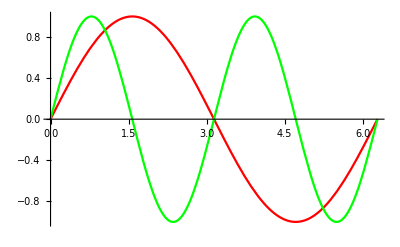

From a purely visual standpoint, these functions do not appear to be perpendicular, so you might not immediately believe that they are orthogonal. Taking the inner product, however, confirms that the functions are orthogonal, as it does indeed give 0. To confirm this for yourself, you can copy the following expression into Mathematica:

Integrate[Sin[x]*Sin[2*x],{x,0,2*Pi}]

and see that you get 0, that these functions are orthogonal. A more helpful way to visually assure ourselves of the orthogonality of two functions would be to graph their product - the integrand of equation (1.16). Trying this out for two sine functions gives us the following result, where a is our arbitrary starting point, λ is our period, and m and n are the orders for the two sine functions. The opaque blue curve represents the integrand of equation (1.16), while the red and green curves represent the individual sine functions, which have been initialized to the previously discussed situation with sin(x) and sin(2x). The result of equation (1.16) is also included above the graph.

Here we can clearly see that the area under the curve (the shaded area) totals to zero when we expect the functions to be orthogonal, but that it totals to some nonzero value when the functions are not orthogonal. Try out adjusting the sliders to convince yourself of these conclusions. Let's take a look next at the orthogonality of two cosine functions:

where the values and curves are all similarly defined and initialized as before. Finally, for sine and cosine:

where we find that sine and cosine are always orthogonal over the same period. Understanding these conclusions will be incredibly important as we move forwards to more complicated, less familiar special functions, such as Bessel or Legendre functions.